## CEPC CDR inputs dated: Oct.30.2017 by Zhen

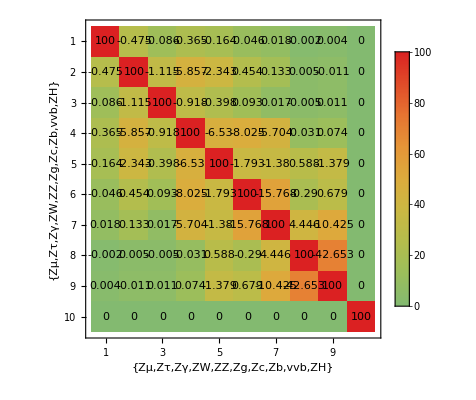

```mathematica
higgsprecepc={15,0.68,8.2,1.2,5.9,1.4,3.5,0.298,3.04,0.50}/100;
inputcorrelations={{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
MatrixPlot[Abs[inputcorrelations],FrameLabel->{{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","vvb","ZH"},{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","vvb","ZH"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[inputcorrelations[[i,j]],{i-0.5,10-j+0.5}],{i,1,10},{j,1,10}]]]
```

## CEPC CDR inputs dated: July.2.2018 by Zhen (based on inputs developed in May) updated July.20.2018 by Kaili

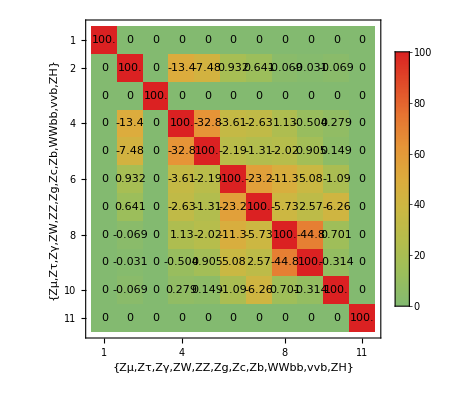

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsobscepcinv=0.155/100;(*used half of the 95% exclusion 0.31 according to Mar.05.2018 result, slide #6 of https://indico.ihep.ac.cn/event/7766/contribution/0/material/slides/0.pdf*)
higgsprecepc=(*July.20.2018; Note that the second to last entry is infinity to avoid double counting*){15.9,0.83,6.62,1.00,5.12,1.28,3.27,0.3179,3.0114,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;

halfcorrelation=(*July.20.2018*)SparseArray[{{11,11}->0,{4,2}->-13.368,{5,2}->-7.478,{6,2}->0.932,{7,2}->0.641,{8,2}->-0.069,{9,2}->-0.031,{10,2}->-0.069,{5,4}->-32.831,{6,4}->-3.613,{7,4}->-2.631,{8,4}->1.125,{9,4}->-0.504,{10,4}->0.279,{6,5}->-2.187,{7,5}->-1.310,{8,5}->-2.020,{9,5}->0.905,{10,5}->0.149,{7,6}->-23.249,{8,6}->-11.335,{9,6}-> 5.081,{10,6}->-1.095,{8,7}-> -5.732,{9,7}-> 2.569,{10,7}-> -6.263,{9,8}-> -44.822,{10,8}-> 0.701,{10,9}-> -0.314}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
MatrixPlot[Abs[inputcorrelations],FrameLabel->{{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"},{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelations[[i,j]],3],{i-0.5,11-j+0.5}],{i,1,11},{j,1,11}]]]
```